```mathematica
fid[t_] := Exp[-R*t]
furrier[w_,t_] :=Exp[-ⅈ*w*t*2*Pi]
wf[tmax_, t_] := Cos[Pi/2/tmax*t]
jf[jc_, t_] := Cos[Pi jc*t]
jfS[jc_, t_] := Sin[Pi jc*t]
spect[R_,w_, tm_, jc_] = Integrate[fid[t]furrier[w,t] wf[tm,t] jf[jc, t],{t,0, tm}] 
spectS[R_,w_, tm_, jc_] = Integrate[fid[t]furrier[w,t] wf[tm,t] jfS[jc, t],{t,0, tm}]
```

(2 ⅇ^(-tm (R+2 ⅈ π w)) tm (π (4 R^2 tm^2+16 ⅈ π R tm^2 w+π^2 (1-4 tm^2 (jc^2+4 w^2))) Cos[jc π tm]+2 tm (R+2 ⅈ π w) (ⅇ^(tm (R+2 ⅈ π w)) (4 R^2 tm^2+16 ⅈ π R tm^2 w+π^2 (1+4 tm^2 (jc^2-4 w^2)))-4 jc π^2 tm Sin[jc π tm])))/((π+2 jc π tm+2 ⅈ R tm-4 π tm w) (π+2 jc π tm-2 ⅈ R tm+4 π tm w) (2 ⅈ R tm+π (-1+2 jc tm-4 tm w)) (-2 ⅈ R tm+π (-1+2 jc tm+4 tm w)))

(2 ⅇ^(-tm (R+2 ⅈ π w)) π tm (2 ⅇ^(tm (R+2 ⅈ π w)) jc tm (4 R^2 tm^2+16 ⅈ π R tm^2 w+π^2 (-1+4 tm^2 (jc^2-4 w^2)))+8 jc π tm^2 (R+2 ⅈ π w) Cos[jc π tm]+(4 R^2 tm^2+16 ⅈ π R tm^2 w+π^2 (1-4 tm^2 (jc^2+4 w^2))) Sin[jc π tm]))/((π+2 jc π tm+2 ⅈ R tm-4 π tm w) (π+2 jc π tm-2 ⅈ R tm+4 π tm w) (2 ⅈ R tm+π (-1+2 jc tm-4 tm w)) (-2 ⅈ R tm+π (-1+2 jc tm+4 tm w)))

```mathematica
spect1[R_,w_, tm_, jc_] = (a1[R,w, tm, jc]+ⅈ b1[R,w, tm, jc])/(c1[R,w, tm, jc] +ⅈ d1[R,w, tm, jc] )
```

```mathematica
spect2[R_,w_, tm_, jc_] = (a1[R,w, tm, jc]*c1[R,w, tm, jc]+b1[R,w, tm, jc]*d1[R,w, tm, jc])/(c1[R,w, tm, jc]^2+d1[R,w, tm, jc]^2) //Simplify
```

```mathematica
spect3[R_,w_, tm_, jc_] =(2 ⅇ^(-R tm) tm ((16 R^4 tm^4+8 π^2 R^2 tm^2 (1+4 jc^2 tm^2-48 tm^2 w^2)+π^4 (16 jc^4 tm^4+(1-16 tm^2 w^2)^2-8 jc^2 (tm^2+16 tm^4 w^2))) (2 tm (ⅇ^(R tm) R (4 R^2 tm^2+π^2 (1+4 jc^2 tm^2-48 tm^2 w^2))-4 jc π^2 R tm Cos[π tm w]^2 Sin[jc π tm]-4 jc π^2 tm Sin[jc π tm] Sin[π tm w] (4 π w Cos[π tm w]-R Sin[π tm w]))+π Cos[jc π tm] ((4 R^2 tm^2+π^2 (1-4 jc^2 tm^2-16 tm^2 w^2)) Cos[2 π tm w]+16 π R tm^2 w Sin[2 π tm w]))+32 π^2 R tm^2 w (-4 R^2 tm^2+π^2 (-1-4 jc^2 tm^2+16 tm^2 w^2)) (4 tm (ⅇ^(R tm) w (-12 R^2 tm^2+π^2 (-1-4 jc^2 tm^2+16 tm^2 w^2))+4 jc π^2 tm w Cos[π tm w]^2 Sin[jc π tm]-4 jc π tm Sin[jc π tm] Sin[π tm w] (R Cos[π tm w]+π w Sin[π tm w]))+Cos[jc π tm] (-16 π R tm^2 w Cos[2 π tm w]+(4 R^2 tm^2+π^2 (1-4 jc^2 tm^2-16 tm^2 w^2)) Sin[2 π tm w]))))/(1024 π^2 R^2 tm^4 w^2 (4 R^2 tm^2+π^2 (1+4 jc^2 tm^2-16 tm^2 w^2))^2+(16 R^4 tm^4+8 π^2 R^2 tm^2 (1+4 jc^2 tm^2-48 tm^2 w^2)+π^4 (16 jc^4 tm^4+(1-16 tm^2 w^2)^2-8 jc^2 (tm^2+16 tm^4 w^2)))^2)
```

(2 ⅇ^(-R tm) tm ((16 R^4 tm^4+8 π^2 R^2 tm^2 (1+4 jc^2 tm^2-48 tm^2 w^2)+π^4 (16 jc^4 tm^4+(1-16 tm^2 w^2)^2-8 jc^2 (tm^2+16 tm^4 w^2))) (2 tm (ⅇ^(R tm) R (4 R^2 tm^2+π^2 (1+4 jc^2 tm^2-48 tm^2 w^2))-4 jc π^2 R tm Cos[π tm w]^2 Sin[jc π tm]-4 jc π^2 tm Sin[jc π tm] Sin[π tm w] (4 π w Cos[π tm w]-R Sin[π tm w]))+π Cos[jc π tm] ((4 R^2 tm^2+π^2 (1-4 jc^2 tm^2-16 tm^2 w^2)) Cos[2 π tm w]+16 π R tm^2 w Sin[2 π tm w]))+32 π^2 R tm^2 w (-4 R^2 tm^2+π^2 (-1-4 jc^2 tm^2+16 tm^2 w^2)) (4 tm (ⅇ^(R tm) w (-12 R^2 tm^2+π^2 (-1-4 jc^2 tm^2+16 tm^2 w^2))+4 jc π^2 tm w Cos[π tm w]^2 Sin[jc π tm]-4 jc π tm Sin[jc π tm] Sin[π tm w] (R Cos[π tm w]+π w Sin[π tm w]))+Cos[jc π tm] (-16 π R tm^2 w Cos[2 π tm w]+(4 R^2 tm^2+π^2 (1-4 jc^2 tm^2-16 tm^2 w^2)) Sin[2 π tm w]))))/(1024 π^2 R^2 tm^4 w^2 (4 R^2 tm^2+π^2 (1+4 jc^2 tm^2-16 tm^2 w^2))^2+(16 R^4 tm^4+8 π^2 R^2 tm^2 (1+4 jc^2 tm^2-48 tm^2 w^2)+π^4 (16 jc^4 tm^4+(1-16 tm^2 w^2)^2-8 jc^2 (tm^2+16 tm^4 w^2)))^2)

```mathematica
spectS3[R,w, tm, jc]//Format[#,CForm]&
```

```mathematica
spectS1[R_,w_, tm_, jc_] = (a2[R,w, tm, jc]+ⅈ b2[R,w, tm, jc])/(c1[R,w, tm, jc] +ⅈ d1[R,w, tm, jc] )
```

```mathematica
spectS2[R_,w_, tm_, jc_] =(b2[R,w, tm, jc]*c1[R,w, tm, jc]-a2[R,w, tm, jc]*d1[R,w, tm, jc])/(c1[R,w, tm, jc]^2+d1[R,w, tm, jc]^2) //Simplify
```

```mathematica
spectS3[R_,w_, tm_, jc_] =((π^4-8 jc^2 π^4 tm^2+8 π^2 R^2 tm^2+16 jc^4 π^4 tm^4+32 jc^2 π^2 R^2 tm^4+16 R^4 tm^4-32 π^4 tm^2 w^2-128 jc^2 π^4 tm^4 w^2-384 π^2 R^2 tm^4 w^2+256 π^4 tm^4 w^4) (32 ⅇ^(-R tm) jc π^3 tm^3 w Cos[jc π tm] Cos[2 π tm w]+64 jc π^2 R tm^4 w Cos[2 π tm w]^2+32 ⅇ^(-R tm) π^2 R tm^3 w Cos[2 π tm w] Sin[jc π tm]-16 ⅇ^(-R tm) jc π^2 R tm^3 Cos[jc π tm] Sin[2 π tm w]-2 ⅇ^(-R tm) π^3 tm Sin[jc π tm] Sin[2 π tm w]+8 ⅇ^(-R tm) jc^2 π^3 tm^3 Sin[jc π tm] Sin[2 π tm w]-8 ⅇ^(-R tm) π R^2 tm^3 Sin[jc π tm] Sin[2 π tm w]+32 ⅇ^(-R tm) π^3 tm^3 w^2 Sin[jc π tm] Sin[2 π tm w]+64 jc π^2 R tm^4 w Sin[2 π tm w]^2)-(32 π^3 R tm^2 w+128 jc^2 π^3 R tm^4 w+128 π R^3 tm^4 w-512 π^3 R tm^4 w^3) (16 ⅇ^(-R tm) jc π^2 R tm^3 Cos[jc π tm] Cos[2 π tm w]-4 jc π^3 tm^2 Cos[2 π tm w]^2+16 jc^3 π^3 tm^4 Cos[2 π tm w]^2+16 jc π R^2 tm^4 Cos[2 π tm w]^2-64 jc π^3 tm^4 w^2 Cos[2 π tm w]^2+2 ⅇ^(-R tm) π^3 tm Cos[2 π tm w] Sin[jc π tm]-8 ⅇ^(-R tm) jc^2 π^3 tm^3 Cos[2 π tm w] Sin[jc π tm]+8 ⅇ^(-R tm) π R^2 tm^3 Cos[2 π tm w] Sin[jc π tm]-32 ⅇ^(-R tm) π^3 tm^3 w^2 Cos[2 π tm w] Sin[jc π tm]+32 ⅇ^(-R tm) jc π^3 tm^3 w Cos[jc π tm] Sin[2 π tm w]+32 ⅇ^(-R tm) π^2 R tm^3 w Sin[jc π tm] Sin[2 π tm w]-4 jc π^3 tm^2 Sin[2 π tm w]^2+16 jc^3 π^3 tm^4 Sin[2 π tm w]^2+16 jc π R^2 tm^4 Sin[2 π tm w]^2-64 jc π^3 tm^4 w^2 Sin[2 π tm w]^2))/((32 π^3 R tm^2 w+128 jc^2 π^3 R tm^4 w+128 π R^3 tm^4 w-512 π^3 R tm^4 w^3)^2+(π^4-8 jc^2 π^4 tm^2+8 π^2 R^2 tm^2+16 jc^4 π^4 tm^4+32 jc^2 π^2 R^2 tm^4+16 R^4 tm^4-32 π^4 tm^2 w^2-128 jc^2 π^4 tm^4 w^2-384 π^2 R^2 tm^4 w^2+256 π^4 tm^4 w^4)^2)
```

((π^4-8 jc^2 π^4 tm^2+8 π^2 R^2 tm^2+16 jc^4 π^4 tm^4+32 jc^2 π^2 R^2 tm^4+16 R^4 tm^4-32 π^4 tm^2 w^2-128 jc^2 π^4 tm^4 w^2-384 π^2 R^2 tm^4 w^2+256 π^4 tm^4 w^4) (32 ⅇ^(-R tm) jc π^3 tm^3 w Cos[jc π tm] Cos[2 π tm w]+64 jc π^2 R tm^4 w Cos[2 π tm w]^2+32 ⅇ^(-R tm) π^2 R tm^3 w Cos[2 π tm w] Sin[jc π tm]-16 ⅇ^(-R tm) jc π^2 R tm^3 Cos[jc π tm] Sin[2 π tm w]-2 ⅇ^(-R tm) π^3 tm Sin[jc π tm] Sin[2 π tm w]+8 ⅇ^(-R tm) jc^2 π^3 tm^3 Sin[jc π tm] Sin[2 π tm w]-8 ⅇ^(-R tm) π R^2 tm^3 Sin[jc π tm] Sin[2 π tm w]+32 ⅇ^(-R tm) π^3 tm^3 w^2 Sin[jc π tm] Sin[2 π tm w]+64 jc π^2 R tm^4 w Sin[2 π tm w]^2)-(32 π^3 R tm^2 w+128 jc^2 π^3 R tm^4 w+128 π R^3 tm^4 w-512 π^3 R tm^4 w^3) (16 ⅇ^(-R tm) jc π^2 R tm^3 Cos[jc π tm] Cos[2 π tm w]-4 jc π^3 tm^2 Cos[2 π tm w]^2+16 jc^3 π^3 tm^4 Cos[2 π tm w]^2+16 jc π R^2 tm^4 Cos[2 π tm w]^2-64 jc π^3 tm^4 w^2 Cos[2 π tm w]^2+2 ⅇ^(-R tm) π^3 tm Cos[2 π tm w] Sin[jc π tm]-8 ⅇ^(-R tm) jc^2 π^3 tm^3 Cos[2 π tm w] Sin[jc π tm]+8 ⅇ^(-R tm) π R^2 tm^3 Cos[2 π tm w] Sin[jc π tm]-32 ⅇ^(-R tm) π^3 tm^3 w^2 Cos[2 π tm w] Sin[jc π tm]+32 ⅇ^(-R tm) jc π^3 tm^3 w Cos[jc π tm] Sin[2 π tm w]+32 ⅇ^(-R tm) π^2 R tm^3 w Sin[jc π tm] Sin[2 π tm w]-4 jc π^3 tm^2 Sin[2 π tm w]^2+16 jc^3 π^3 tm^4 Sin[2 π tm w]^2+16 jc π R^2 tm^4 Sin[2 π tm w]^2-64 jc π^3 tm^4 w^2 Sin[2 π tm w]^2))/((32 π^3 R tm^2 w+128 jc^2 π^3 R tm^4 w+128 π R^3 tm^4 w-512 π^3 R tm^4 w^3)^2+(π^4-8 jc^2 π^4 tm^2+8 π^2 R^2 tm^2+16 jc^4 π^4 tm^4+32 jc^2 π^2 R^2 tm^4+16 R^4 tm^4-32 π^4 tm^2 w^2-128 jc^2 π^4 tm^4 w^2-384 π^2 R^2 tm^4 w^2+256 π^4 tm^4 w^4)^2)

```mathematica
(* commond divisor *)
dv1[R_,w_, tm_, jc_] = π^4-8 jc^2 π^4 tm^2+8 π^2 R^2 tm^2+16 jc^4 π^4 tm^4+32 jc^2 π^2 R^2 tm^4+16 R^4 tm^4-32 π^4 tm^2 w^2-128 jc^2 π^4 tm^4 w^2-384 π^2 R^2 tm^4 w^2+256 π^4 tm^4 w^4+ⅈ (32 π^3 R tm^2 w+128 jc^2 π^3 R tm^4 w+128 π R^3 tm^4 w-512 π^3 R tm^4 w^3)
```

```mathematica
c1[R_,w_, tm_, jc_] = π^4-8 jc^2 π^4 tm^2+8 π^2 R^2 tm^2+16 jc^4 π^4 tm^4+32 jc^2 π^2 R^2 tm^4+16 R^4 tm^4-32 π^4 tm^2 w^2-128 jc^2 π^4 tm^4 w^2-384 π^2 R^2 tm^4 w^2+256 π^4 tm^4 w^4
```

```mathematica
d1[R_,w_, tm_, jc_] = 32 π^3 R tm^2 w+128 jc^2 π^3 R tm^4 w+128 π R^3 tm^4 w-512 π^3 R tm^4 w^3
```

```mathematica
a2[R_,w_, tm_, jc_] = 16 ⅇ^(-R tm) jc π^2 R tm^3 Cos[jc π tm] Cos[2 π tm w]-4 jc π^3 tm^2 Cos[2 π tm w]^2+16 jc^3 π^3 tm^4 Cos[2 π tm w]^2+16 jc π R^2 tm^4 Cos[2 π tm w]^2-64 jc π^3 tm^4 w^2 Cos[2 π tm w]^2+2 ⅇ^(-R tm) π^3 tm Cos[2 π tm w] Sin[jc π tm]-8 ⅇ^(-R tm) jc^2 π^3 tm^3 Cos[2 π tm w] Sin[jc π tm]+8 ⅇ^(-R tm) π R^2 tm^3 Cos[2 π tm w] Sin[jc π tm]-32 ⅇ^(-R tm) π^3 tm^3 w^2 Cos[2 π tm w] Sin[jc π tm]+32 ⅇ^(-R tm) jc π^3 tm^3 w Cos[jc π tm] Sin[2 π tm w]+32 ⅇ^(-R tm) π^2 R tm^3 w Sin[jc π tm] Sin[2 π tm w]-4 jc π^3 tm^2 Sin[2 π tm w]^2+16 jc^3 π^3 tm^4 Sin[2 π tm w]^2+16 jc π R^2 tm^4 Sin[2 π tm w]^2-64 jc π^3 tm^4 w^2 Sin[2 π tm w]^2
b2[R_,w_, tm_, jc_] = (32 ⅇ^(-R tm) jc π^3 tm^3 w Cos[jc π tm] Cos[2 π tm w]+64 jc π^2 R tm^4 w Cos[2 π tm w]^2+32 ⅇ^(-R tm) π^2 R tm^3 w Cos[2 π tm w] Sin[jc π tm]-16 ⅇ^(-R tm) jc π^2 R tm^3 Cos[jc π tm] Sin[2 π tm w]-2 ⅇ^(-R tm) π^3 tm Sin[jc π tm] Sin[2 π tm w]+8 ⅇ^(-R tm) jc^2 π^3 tm^3 Sin[jc π tm] Sin[2 π tm w]-8 ⅇ^(-R tm) π R^2 tm^3 Sin[jc π tm] Sin[2 π tm w]+32 ⅇ^(-R tm) π^3 tm^3 w^2 Sin[jc π tm] Sin[2 π tm w]+64 jc π^2 R tm^4 w Sin[2 π tm w]^2)
```

```mathematica
tmp= ⅇ^(-tm (R+2 ⅈ π w))=Exp[-tm R]*(Cos[2 π w tm]- ⅈ Sin[2 π w tm])
tmpP = ⅇ^(tm (R+2 ⅈ π w))=Exp[tm R]*(Cos[2 π w tm]+ ⅈ Sin[2 π w tm])
(*
http://modular.math.washington.edu/20b/notes/html/node30.html
*)
```

```mathematica
Format[spect[R,w, tm, jc] ,InputForm];
```

```mathematica
spectS3[10., 10, 0.8, 3.0]
```

-0.000758311

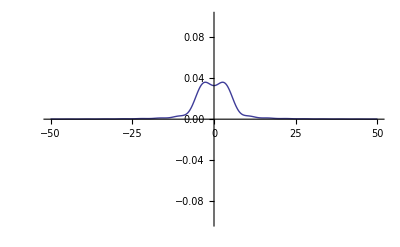

```mathematica
Plot[spect3[10., x, 0.18, 6.0],{x,-50,50.0}, PlotRange->{-0.1,0.1}]
```

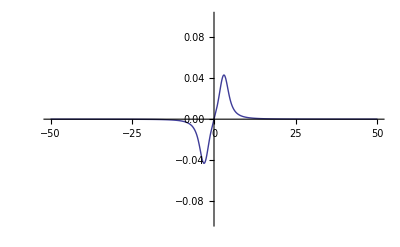

```mathematica
Plot[-1*spectS3[10., x, 0.55, 6.0],{x,-50,50.0}, PlotRange->{-0.1,0.1}]
```

```mathematica
Sum[spect3[10., x, 0.25, 6.0]//Re,{x,-100,100.0}]
```

0.494955

```mathematica
D[spectS3[R,w, tm, jc],tm] //Simplify
```

```mathematica
t1m = 0.61
FindMaximum[1/Sqrt[t1m]*spect3[10., x, t1m, 6.0]//Re,{x,3.0}]
```

0.61

{0.0643599,{x→2.96003}}

```mathematica
step=0.002; MaxN = 200;
ttS=Table[FindMaximum[-1/Sqrt[k*step]*spectS3[10., x, k*step, 6.0],{x,3.0}],{k,1,MaxN,1}];
tt=Table[FindMaximum[1/Sqrt[k*step]*spect3[10., x, k*step, 6.0],{x,3}],{k,1,MaxN,1}];
```

FindMaximum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: "lstol" will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: "lstol" will be suppressed during this calculation.

```mathematica
tt[[MaxN]][[1]]
```

0.0743927

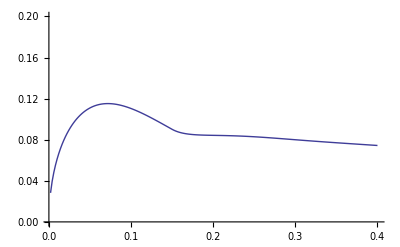

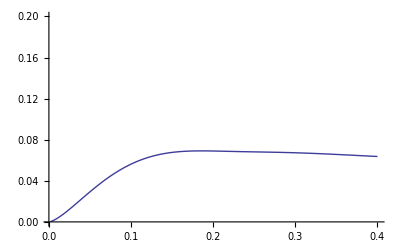

```mathematica
opt = Table[{k*step,tt[[k]][[1]]},{k,1,MaxN,1}];
optS = Table[{k*step,ttS[[k]][[1]]},{k,1,MaxN,1}];
tim=Table[k*step,{k,1,MaxN,1}];
ListLinePlot[opt, PlotRange->{0.,0.2}]
ListLinePlot[optS, PlotRange->{0.,0.2}]
```

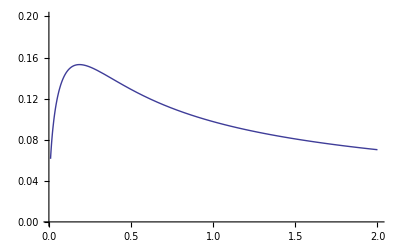

```mathematica
Plot[1/Sqrt[t1]*sp[10., 0, t1]//Re,{t1,0.01,2.0}, PlotRange->{0.,0.2}]
```

```mathematica
optim[R_,t1_]=1/Sqrt[t1]*sp[R, 0, t1]
```

(2 √t1 (ⅇ^(-R t1) π+2 R t1))/(π^2+4 R^2 t1^2)

```mathematica
dr[R_,x_]=D[optim[R,x],x]
```

-(16 R^2 x^(3/2) (ⅇ^(-R x) π+2 R x))/((π^2+4 R^2 x^2)^2)+(2 (2 R-ⅇ^(-R x) π R) √x)/(π^2+4 R^2 x^2)+(ⅇ^(-R x) π+2 R x)/(√x (π^2+4 R^2 x^2))

```mathematica
dr[R,t]
```

-(16 R^2 t^(3/2) (ⅇ^(-R t) π+2 R t))/((π^2+4 R^2 t^2)^2)+(2 (2 R-ⅇ^(-R t) π R) √t)/(π^2+4 R^2 t^2)+(ⅇ^(-R t) π+2 R t)/(√t (π^2+4 R^2 t^2))

```mathematica
NSolve[dr[10.,t]==0,t]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

NSolve[-(1600. t^(3/2) (ⅇ^(-10. t) π+20. t))/((π^2+400. t^2)^2)+(2 (20.-31.4159 ⅇ^(-10. t)) √t)/(π^2+400. t^2)+(ⅇ^(-10. t) π+20. t)/(√t (π^2+400. t^2))==0,t]

```mathematica
FindRoot[dr[10.,t]==0,{t,0.2}]
```

{t→0.186153}

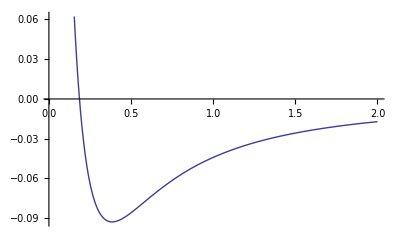

```mathematica
Plot[dr[10.,t1],{t1,0.01,2.0}]
```

```mathematica
(c-d*ⅈ)*(a+b*ⅈ)/((c+d*ⅈ) (c-d*ⅈ)) //Expand//Simplify
```

(a+ⅈ b)/(c+ⅈ d)

```mathematica
(c-d*ⅈ)*(a+b*ⅈ)//Expand
```

a c+ⅈ b c-ⅈ a d+b d

```mathematica
((c+d*ⅈ) (c-d*ⅈ))//Expand
```

c^2+d^2

```mathematica
(a c+ⅈ b c-ⅈ a d+b d)/(c^2+d^2) //Simplify
```

(a+ⅈ b)/(c+ⅈ d)